```mathematica
ClearAll["Global'*"]
$PrePrint = MatrixForm
```

MatrixForm

```mathematica
G=.01;
H=1;
rho0=1;
ymax=10;
v0[y_]:=(H y)
rho0y[y_]:=(rho0 + 0.1 Sin[2Pi y / 20])
m[y_]:=(Integrate[rho0y[yy],{yy,0,y}])
ksi[y_,t_]:=(y+v0[y]t-2Pi G m[y]t^2)
a[t_]:=1+H t- 2 Pi G rho0 t^2

ksiDy[y_,t_]:=(1+H t-2Pi G rho0y[y] t^2)
ksiDt[y_,t_]:=(v0[y]-4Pi G m[y]t)

rhokt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k ksi[y,t]],{y,-ymax,ymax}]
)

vkt[k_,t_]:=(
NIntegrate[ksiDt[y,t]Exp[-I k ksi[y,t]]ksiDy[y,t],{y,-ymax,ymax}]
)

rhoScaledkt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k / a[t]   ksi[y,t]],{y,-ymax,ymax}])
```

```mathematica
tmax=Max[t/.{Solve[ksi[-ymax,t]==0,t][[2]],Solve[ksi[ymax,t]==0,t][[2]]}];
tbounce=Max[t/.{Solve[ksiDt[-ymax,t]==0,t][[1]],Solve[ksiDt[ymax,t]==0,t][[1]]}];
tstep=.05;
ts=Table[t,{t,0,tmax,tstep}];
k=1;

rhoScaledk1=rhoScaledkt[k,ts];
(*rhok1=rhokt[k,ts];
v1=vkt[k,ts];*)
```

```mathematica
ListLinePlot[Thread[{ts,Re[rhoScaledk1]}],PlotLabels->{"Re"}, PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Im[rhoScaledk1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Abs[rhoScaledk1]^2}],PlotLabels->{"Modul kwadrat"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red}},None}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Thread[{ts,Re[rhok1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Im[rhok1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Abs[rhok1]^2}],PlotLabels->{"Modul kwadrat"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Re[v1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
ListLinePlot[Thread[{ts,Im[v1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
```

```mathematica
Plot3D[ksi[y,t],{y,-ymax,ymax},{t,0,tmax},PlotRange->All,AxesLabel->{"y","t"}]
```

-Graphics3D-

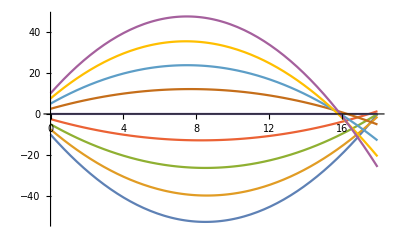

```mathematica
ysToPlot=Table[y,{y,-ymax,ymax,2.5}];
Plot[Evaluate@Table[ksi[y,t],{y,-ymax,ymax,2.5}],{t,0,tmax}]
```

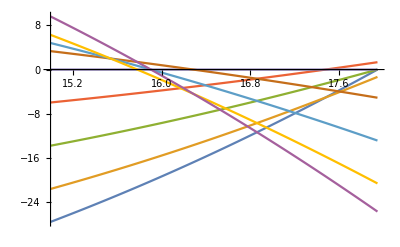

```mathematica
Plot[Evaluate@Table[ksi[y,t],{y,-ymax,ymax,2.5}],{t,15,tmax}]
```

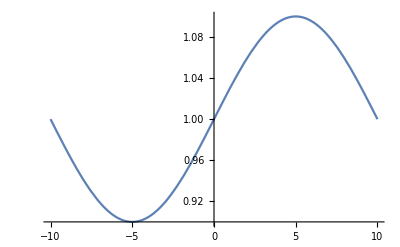

```mathematica
Plot[rho0y[y],{y,-ymax,ymax}]
```

```mathematica
InverseFunction[ksi]
```

ksi^(-1)

```mathematica
rhoScaled[x_,t_]:=(rho0y[x/a[t]]);
Plot3D[rhoScaled[x,t],{x,-ymax*a[tmax],ymax*a[tmax]},{t,0,tmax},AxesLabel->{"x","t"},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[ksiDy[y,t],{y,-ymax,ymax},{t,0,tmax},PlotRange->All,AxesLabel->{"y","t"}]
```

-Graphics3D-

```mathematica
rhotx[t_,x_]:=(rho0y[Max[y/.Solve[ksi[y,t]==x]]])
Plot[rhotx[1,x],{x,0,1}]
```

```mathematica
tt=1;
xx=1;
```

ReplaceAll::reps: {NSolve[2 yy-0.0628319 (yy+0.63662 Power[«2»])==1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NSolve[2. yy-0.0628319 (yy+0.63662 Power[«2»])==1.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

rho0y[yy/.NSolve[2. yy-0.0628319 (yy+0.63662 Sin[0.15708 yy]^2)==1.],yy]

```mathematica
yy/.Solve[ksi[yy,1]==1,yy]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[2 yy-0.0628319 (yy+0.63662 Power[«2»])==1,yy]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

yy/.Solve[2 yy-0.0628319 (yy+0.63662 Sin[(π yy)/20]^2)==1,yy]